# Quantum Magnets + Impurity

This script employs exact diagonalization to compute the magnon spectrum and spin expectation values in various Quantum Magnets featuring a magnetic impurity (adatom) coupled to a single site. These materials are effectively modeled by the JKΓ extended Kitaev model.
	> we will focus mainly in two materials:  Subscript[RuCl, 3]  (e.g. 1706.06113 ) and Subscript[CrI, 3] (e.g. 1704.03849 )

## Preamble

```mathematica
Needs["MaTeX`"]
```

```mathematica
If[ FileNames@NotebookDirectory[]!=FileNames@Directory[],SetDirectory[NotebookDirectory[]] ];

Get[ FileNameJoin[{Directory[],"definitions.wl" }] ]
```

## Code

For small system sizes Lx,Ly < 3 on can run the code here, but the idea is to run it on the cluster

## Figures

### Kitaev FM (2,2)

Information/Parameters

```mathematica
HamCoupling="Kitaev_FM";
dataName="JK_Range[0,1,.1]";
systemDimensions = {{2,2}};
kitaev           = {{-1,-1,-1}};
heisenberg       = {0{1,1,1}};
anisotropy       = {0{1,1,1}};
hfields          = {0.4 cvec};
impuritySpin     = {1/2};
gs               = {1};
KondoCouplings   = Range[0,1,.1];
parameters       = N@Tuples[{systemDimensions,kitaev,heisenberg,anisotropy,hfields,impuritySpin,gs} ];
klevels          = 50;
```

Reading eigenvalue data

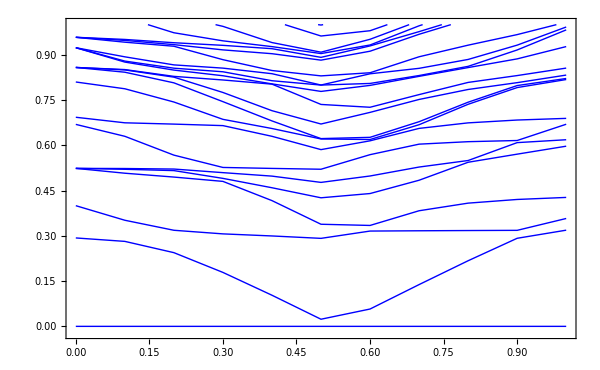

```mathematica
Module[{Lx,Ly,J,λn,Simp,K,h,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend},

	{{Lx,Ly},K,J,λn,h,Simp,g}=parameters[[1]]; 
	{Lx,Ly}=Round@{Lx,Ly};
	
	datapath     =  dataPath[dataName,HamCoupling,Simp,{Lx,Ly}];
	eValues       =  dataRead[datapath[[2]]];

	plotTitle  = "\\text{Kitaev FM - } (L_x,L_y)=(2,2)" ;
	plotLegend= "S_{\\text{imp}}=1/2, \\, \\mathbf{h}=0.4 \\, \\mathbf{c}";
	fig1             = 
ListPlot[Transpose[Thread/@eValues],PlotStyle->{{Blue,Thick}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],PlotLabel->(MaTeX[#,Magnification->2]&)@plotTitle, PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1]&)@plotLegend },LegendMarkers->Automatic,LegendFunction->"Panel"],{Scaled[{.98,.98}], Scaled[{1, 1}]}]
(*LineLegend[Placed[(MaTeX[#,Magnification->2]&)@plotLegend ,{Scaled[{0,0.5}], {0, 0.5}}] ,LegendFunction->"Panel"]*),
FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/K","\\omega/K"},ImageSize->600,PlotRange->{-.02,1}]
]
```

### Kitaev FM (3,2)

Information/Parameters

```mathematica
HamCoupling="Kitaev_FM";
dataName="JK_Range[0,1,.1]";
systemDimensions = {{3,2}};
kitaev           = {{-1,-1,-1}};
heisenberg       = {0{1,1,1}};
anisotropy       = {0{1,1,1}};
hfields          = {0.4 cvec};
impuritySpin     = {1/2};
gs               = {1};
KondoCouplings   = Range[0,1,.1];
parameters       = N@Tuples[{systemDimensions,kitaev,heisenberg,anisotropy,hfields,impuritySpin,gs} ];
klevels          = 50;
```

Reading eigenvalue data

```mathematica
Module[{Lx,Ly,J,λn,Simp,K,h,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend},

	{{Lx,Ly},K,J,λn,h,Simp,g}=parameters[[1]]; 
	{Lx,Ly}=Round@{Lx,Ly};
	
	datapath     =  dataPath[dataName,HamCoupling,Simp,{Lx,Ly}];
	eValues       =  dataRead[datapath[[2]]];

	plotTitle  = "\\text{Kitaev FM - } (L_x,L_y)=(3,2)" ;
	plotLegend= "S_{\\text{imp}}=1/2, \\, \\mathbf{h}=0.4 \\, \\mathbf{c}";
	fig1             = 
ListPlot[Transpose[Thread/@eValues],PlotStyle->{{Blue,Thick}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],PlotLabel->(MaTeX[#,Magnification->2]&)@plotTitle, PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1]&)@plotLegend },LegendMarkers->Automatic,LegendFunction->"Panel"],{Scaled[{.98,.98}], Scaled[{1, 1}]}]
(*LineLegend[Placed[(MaTeX[#,Magnification->2]&)@plotLegend ,{Scaled[{0,0.5}], {0, 0.5}}] ,LegendFunction->"Panel"]*),
FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/K","\\omega/K"},ImageSize->600,PlotRange->{-.02,1}]
]
```

## Spin operators

Compute expectation values of spin operators. 
First take component along the c direction.

```mathematica
Ns=30;
JKmax=1;
dJK=JKmax/Ns;
For[i=0,i≤Ns,i++,
JK0=i dJK;
R=Chop[Eigensystem[N[H[JK0]]]];
sortR=SortBy[Table[{R[[1,i]],R[[2,i]]},{i,1,Length[H[JK0]]}],First];
Ψ[n_]:=sortR[[n,2]];
Mimp=Conjugate[Ψ[1]].KroneckerProduct[Id,Id,Id,Id,Id,Id,Id,Id,Sum[cvec[[n]] Subscript[S, n],{n,1,3}]].Ψ[1];
Mbulk=Conjugate[Ψ[1]].KroneckerProduct[Id,Id,Id,Id,Id,Id,Id,Sum[cvec[[n]] 1/2 Subscript[σ, n],{n,1,3}],IdS].Ψ[1];
Mimplist[i]=Chop[N[{JK0,Mimp}]];
Mbulklist[i]=Chop[N[{JK0,Mbulk}]]];
listMimp=Table[Mimplist[i],{i,0,Ns}];
listMbulk=Table[Mbulklist[i],{i,0,Ns}];
```

```mathematica
ListPlot[{listMimp,listMbulk},PlotStyle->{Blue,Red},Joined->False,Frame->True,PlotRange->All,FrameStyle->Directive[Black,16,Thickness[.002]],FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/K","\\langle \\mathbf S\\cdot \\hat{\\mathbf{c}}\\rangle"},ImageSize->450,PlotLegends->Placed[(MaTeX[#,Magnification->1.8]&)/@{"\\text{impurity}","\\text{bulk}"},{.8,.8}]]
```

Now the in-plane component along the a direction. 
This component is always zero for the impurity spin and the site to which it is coupled. 
Consider  j=3 as a neighboring site that shows the vortex-like pattern.

```mathematica
dJK=JKmax/Ns;
For[i=0,i≤Ns,i++,
JK0=i dJK;
R=Chop[Eigensystem[N[H[JK0]]]];
sortR=SortBy[Table[{R[[1,i]],R[[2,i]]},{i,1,Length[H[JK0]]}],First];
Ψ[n_]:=sortR[[n,2]];
Mimp=Conjugate[Ψ[1]].KroneckerProduct[Id,Id,Id,Id,Id,Id,Id,Id,Sum[avec[[n]] Subscript[S, n],{n,1,3}]].Ψ[1];
Mneigh=Conjugate[Ψ[1]].KroneckerProduct[Id,Id,Sum[avec[[n]] 1/2 Subscript[σ, n],{n,1,3}],Id,Id,Id,Id,Id,IdS].Ψ[1];
Mimplist[i]=Chop[N[{JK0,Mimp}]];
Mneighlist[i]=Chop[N[{JK0,Mneigh}]]];
listMimp=Table[Mimplist[i],{i,0,Ns}];
listMneigh=Table[Mneighlist[i],{i,0,Ns}];
```

```mathematica
ListPlot[{listMimp,listMneigh},PlotStyle->{Blue,Magenta},Joined->False,Frame->True,FrameStyle->Directive[Black,16,Thickness[.002]],FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/K","\\langle \\mathbf S\\cdot \\hat{\\mathbf{a}}\\rangle"},ImageSize->450,PlotLegends->Placed[(MaTeX[#,Magnification->1.8]&)/@{"\\text{impurity}","\\text{bulk}, j=3"},{.8,.7}]]
```